```mathematica
link=Install[LinkConnect["46203@192.168.150.130,46149@192.168.150.130",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωhe=1/4,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θbp=0.045,θbhe=0.0225,ωbp=15*Sqrt[0.5],ωbhe=7.5*Sqrt[0.4],ωe=150,
ωp ={0.0266,
0.1207,
0.3312,
0.5934,
0.8158,
0.9859,
1.1178,
1.2203,
1.2975,
1.3516,
1.3836,
1.3943,
1.3836,
1.3516,
1.2975,
1.2203,
1.1178,
0.9859,
0.8158,
0.5934,
0.3312,
0.1207,
0.0266},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd*2.25/2.025,vr*2.25/2.025]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe,Ωhe},{ωbp,ωe,ωbhe},{θbp,θe,θbhe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
check=With[{k=9.9,wna=87.6Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[5.3,0.01] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

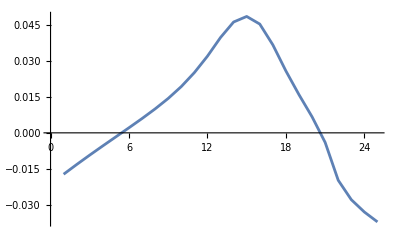

```mathematica
sol1=With[{k=Range[2.2,1.8,-0.05],wna=88.6Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[2.25,3.0,0.05],wna=88.6Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[2.0,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]];
sol=Join[sol1,sol2[[2,2]]];
ListLinePlot[Im[sol]]
```

```mathematica
Export["vs=2.25,87.6,0.5h0.4he-0.045-im-5,9.2-12.0.csv",Im[sol]];

Export["vs=2.25,87.6,0.5h0.4he-0.045-re-5,9.2-12.0.csv",Re[sol]];
```

```mathematica
r=Complex[2.0,0.03] ;
dk=0.05;
kl=1.8;
kmid=2.2;
kr=3.0;
dwna=0.1Degree;
wnai=86.8Degree;
wnamid=88Degree;
wnaf=89.4Degree;
a2={};
With[{k=Range[kmid,kl,-dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r(1+0.0001 I {0,1,2}),MaxIterations->100];
a2=Append[a2,Im[sol[[2,2]]]],{wna,wnamid,wnaf,dwna}]];
a1={};
With[{k=Range[kmid+dk,kr,dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r (1+0.0001 I {0,1,2}),MaxIterations->100];
a1=Append[a1,Im[sol[[2,2]]]],{wna,wnamid,wnaf,dwna}]];
a3={};
With[{k=Range[kmid,kl,-dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r (1+0.0001 I {0,1,2}),MaxIterations->100];
a3=Append[a3,Im[sol[[2,2]]]],{wna,wnamid-dwna,wnai,-dwna}]];
a4={};
With[{k=Range[kmid+dk,kr,dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r(1+0.0001 I {0,1,2}),MaxIterations->100];
a4=Append[a4,Im[sol[[2,2]]]],{wna,wnamid-dwna,wnai,-dwna}]];
```

```mathematica
ra2=Map[Reverse,a2];
a1;
toup=Join[ra2,a1,2];
ra3=Map[Reverse,a3];
a4;
todown=Join[ra3,a4,2];
rtodown=Reverse[todown];
```

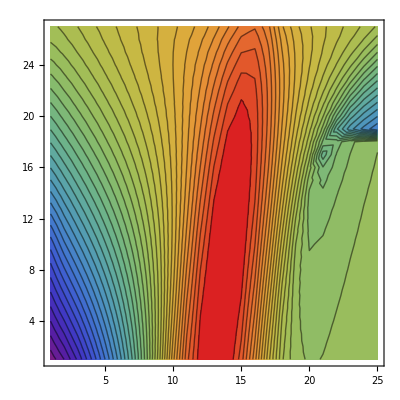

0.0519622

```mathematica
total=Join[rtodown,toup];
 ListContourPlot[total,ColorFunction->"Rainbow",Contours->40]
Export["vs=2.25-0.9h-0.045-2.8-3.0,86.8-89.5-.csv",total];
Max[total]
```